# Mathlink example

## Definitions

```mathematica
DiscretePowerLawDistributionPDF[α_,xMin_,x_]:=x^-α/HurwitzZeta[α,xMin];
DiscretePowerLawDistributionPDF[α_,xMin_,xMax_,x_]:=x^-α/(HurwitzZeta[α,xMin]-HurwitzZeta[α,1+xMax]);;
DiscretePowerLawDistributionCDF[α_,xMin_,x_]:=HurwitzZeta[α,x]/HurwitzZeta[α,xMin];
DiscretePowerLawDistributionCDF[α_,xMin_,xMax_,x_]:=(HurwitzZeta[α,x]-HurwitzZeta[α,1+xMax])/(Zeta[α,xMin]-Zeta[α,1+xMax]);
GeneratePowerlawSampleData[α_,xMin_,xMax_,sampleSize_ :1000]:=Block[{dist},
dist = ProbabilityDistribution[DiscretePowerLawDistributionPDF[α,xMin,xMax,x],{x,xMin,xMax,1}];

RandomVariate[dist,sampleSize]

];
```

```mathematica
HistogramPoints[data_]:=Map[{#,N[Count[data,#]/Length[data]]}&,Sort[DeleteDuplicates[data]]];
HistogramPointPlots[data_List,opts: OptionsPattern[]]:=Block[{pltData = HistogramPoints[data]},
ListPlot[
pltData,
Joined->False,
Frame->True,
PlotTheme->"Monochrome",
BaseStyle->FontSize->14,
PlotStyle->{PointSize[Large],ColorData["Legacy"]["IndianRed"]},
ImageSize->500,
PlotMarkers->None,
GridLines->{Automatic,All},
GridLinesStyle->Directive[Gray,Opacity[0.3]],
FilterRules[{opts},Options[ListPlot]]
]
];
```

## Link usage

### Import link

```mathematica
buildDirectory = "cmake-build-release_mathlink";
link = Install[FileNameJoin[{ParentDirectory[NotebookDirectory[]],buildDirectory,"PowerLawFitterCpp"}]]
```

LinkObject[…]

### Functions defined in the link

```mathematica
Column@LinkPatterns[link]
```

SetAlphaPrecision[precision_Real]
PowerlawFitModel[data_List,distributionType_String]
PowerlawFitModel[data_List,xParameter_Integer,distributionType_String]
PowerlawGoodnessOfFit[data_List,replicas_Integer]
PowerlawGoodnessOfFit[data_List,replicas_Integer,xParameter_Integer,distributionType_String,syntheticGeneratorMode_String]

### Options

distributionType can take two values: “LeftBounded” and “RightBounded”.
syntheticGeneratorMode can also be either: “FullParametric” or “SemiParametric”.

### Usage

Sample from a model distribution.

```mathematica
sample = GeneratePowerlawSampleData[2.5,1,100,300]
```

{1,5,1,1,1,1,1,1,1,1,1,1,1,1,3,1,1,1,5,2,1,1,1,1,2,2,1,1,1,3,1,1,2,1,1,1,1,1,1,1,2,1,1,1,2,2,2,1,1,2,1,1,1,2,1,1,1,1,2,1,1,2,2,1,2,3,1,1,1,1,1,2,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,4,1,1,1,1,1,1,2,1,5,1,1,2,1,1,3,1,1,1,1,1,1,2,1,1,3,1,1,1,1,1,1,1,1,1,2,1,1,2,2,4,3,7,28,1,1,1,1,4,4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,5,1,2,1,2,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,3,1,2,1,2,1,1,1,1,1,1,1,1,2,2,2,2,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,3,1,2,1,1,1,1,1,3,1,2,1,6,5,1,1,1,1,2,1,1,1,1,3,1,2,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,4,2,1,1,1,1,1,1,1,1,1,1,3,1,1,1,2,15,1,1,1,1,1,1,1,1,1,1,3,1,5,19,3,1,1,4,2,1,1,1,14,1,1,1,2,10,4,2,1,1}

Sampe from empirical data.

```mathematica
sample = {12,1,4,1,10,14,1,1,1,1,1,2,91,3,1,1,3,1,16,1,1,1,22,37,1,6,7,18,1,1,2,1,2,6,2,3,1,1,3,3,17,1,1,1,1,1,4,1,4,20,1,1,8,1,15,4,2,4,7,1,1,6,1,1,2,1,1,4,2,1,12,2,1,1,1,1,46,48,10,1,11,1,9,1,2,73,1,1,1,1,1,3,6,9,55,1,1,1,1,1,1,1,16,1,4,1,50,53,6,6,1,6,1,1,1,18,1,4,1,54,29,1,1,1,47,17,1,1,11,1,11,1,3,1,11,3,11,3,2,1,50,1,8,16,4,1,1,9,2,2,1,1,2,4,83,1,5,1,1,1,1,3,4,1,1,1,1,5,1,6,2,1,9,2,2,4,7,2,1,1,1,5,10,5,7,1,2,1,9,1,1,2,1,1,15,1,1,1,1,15,1,2,15,2,1,1,1,1,3,4,3,1,4,1,2,1,2,1,12,1,1,1,8,2,1,1,1,2,1,1,1,1,14,1,1,1,1,8,3,1,2,2,11,1,16,1,1,1,1,8,1,78,7,3,31,11,4,1,1,1,8,12,1,2,1,1,3,1,4,1,93,1,2,1,19,11,7,4,1,4,2,7,1,1,11,3,1,1,13,11,1,5,2,2,2,1,1,1,51,3,1,2,3,1,1,1,1,2,4,3,1,1,1,1,1,1,1,1,1,1,3,1,1,1,1,7,1,2,1,6,45,1,1,1,6,36,1,1,6,1,1,1,86,9,38,1,3,4,1,4,1,3,1,1,1,1,7,2,20,3,1,1,1,7,1,1,1,60,1,5,1,1,6,1,1,29,1,1,14,1,1,1,9,1,1,1,1,1,1,5,7,3,1,42,1,15,14,6,1,1,9,2,3,25,1,1,3,1,1,1,1,15,11,9,1,1,3,16,19,1,2,1,2,1,2,2,1,1,2,2,1,1,12,1,1,10,1,1,1,1,2,1,6,2,1,1,29,12,1,1,3,1,1,61,1,4,1,5,1,1,1,1,75,10,2,64,1,1,8,3,1,6,1,1,3,1,1,60,1,1,1,2,9,3,1,4,1,2,1,2,1,1,1,5,83,1,5,1,1,1,1,3,1,52,1,15,1,4,6,3,1,3,4,9,13,14,1,1,2,1,3,4,1,1,1,1,45,7,5,1,9,1,9,1,1,3,15,5,1,6,1,2,3,1,4,3,1,2,3,4,3,2,1,1,1,12,1,47,1,91,1,1,1,1,1,37,1,9,3,3,4,1,1,1,1,2,1,3,6,1,5,1,1,1,1,4,17,3,1,4,2,1,1,1,2,2,2,1,1,1,18,29,19,1,6,1,1,18,1,53,1,6,1,1,12,23,1,1,1,1,1,17,1,1,15,2,2,6,2,2,1,1,1,1,2,1,2,1,1,1,1,1,44,9,2,3,1,1,3,3,1,1,1,5,1,12,2,1,1,1,1,1,2,1,4,1,1,10,1,29,18,13,14,1,5,1,1,1,7,3,1,1,1,1,8,11,8,1,1,1,1,4,1,1,5,52,2,14,15,22,1,2,1,18,11,1,1,1,1,13,1,1,1,9,1,1,1,3,1,23,2,37,5,1,1,7,1,1,57,1,28,1,1,1,3,1,1,1,2,1,4,55,7,1,11,7,1,1,1,2,4,88,1,3,8,10,1,15,1,8,1,10,1,2,1,1,3,1,1,1,1,4,1,3,4,2,2,1,2,35,2,3,2,55,1,1,1,1,1,13,1,1,1,1,1,3,1,9,7,1,30,2,1,2,5,6,12,1,21,1,7,2,1,1,1,9,1,1,4,1,1,58,16,1,6,1,3,2,1,1,1,1,47,1,5,1,3,2,2,1,2,7,1,1,8,65,1,1,1,1,1,4,2,1,67,2,1,2,1,2,4,1,1,1,1,1,1,4,1,2,1,1,1,2,1,61,1,10,1,7,1,1,2,2,1,1,1,1,1,31,17,1,1,23,1,3,1,1,2,1,4,6,1,10,1,1,1,20,2,1,1,2,4,2,1,2,85,1,1,1,1,75,45,7,1,3,1,3,1,3,1,2,10,1,1,3,3,1,4,1,1,3,1,1,1,78,1,1,7,2,5,1,1,3,2,1,1,1,30,3,1,10,1,3,1,1,2,4,3,1,10,1,1,2,1,1,3,1,3,1,1,1,1,1,1,69,3,2,1,1,1,1,5,1,1,58,10,6,1,8,1,2,8,5,3,2,1,16,1,2,1,20,1,1,1,4,1,1,1,5,2,2,1,1,1,1,2,4,1,32,7,8,27,1,1,77,10,10,1,1,2,2,1,5,1,2,1,5,49,8,9,1,1,9,14,70,3,1,1,3,1,51,1,1,1,10,1,1,1,1,1,1,1,3,1,1,69,1,1,1,1,1,1,64,2,1,3,1,1,1,1,74,1,1,2,1,3,7,4,86,1,3,1,1,1,1,61,22,1,1,3,1,1,1,1,62,3,10,2,1,1,11,1,1,1,73,1,2,2,1,1,48,4,18,1,1,27,1,7,3,10,1,2,7,7,7,2,1,2,2,1,1,2,3,1,1,1,10,1,1,2,2,3,1,7,1,2,13,74,1,3,1,1,1,1,15,2,20,1,1,1,1,1,2,1,5,2,2,1,1,1,1,1,50,3,6,1,2,31,36,3,4,1,1,1,2,4,1,1,1,2,41,3,3,1,1,1,24,3,1,1,1,16,4,10,5,1,1,1,7,1,1,1,29,1,1,2,1,1,7,8,3,1,3,21,1,1,2,1,2,1,30,1,1,1,2,1,1,56,1,1,1,10,1,17,10,9,19,3,6,1,1,1,1,4,1,1,2,4,45,1,18,1,6,1,3,1,1,1,1,1,3,70,17,1,3,1,3,3,1,1,13,1,3,1,1,5,1,2,13,1,1,1,4,1,6,4,2,5,1,3,1,1,1,1,1,3,1,1,1,3,1,1,33,2,1,8,4,4,1,19,1,1,1,1,5,19,1,2,1,6,7,2,27,1,9,1,1,1,81,1,1,1,1,4,5,1,1,1,2,7,1,1,1,1,1,6,1,28,1,1,2,9,1,1,2,1,1,3,1,7,5,3,12,2,4,1,1,3,5,26,1,2,2,1,1,4,1,1,1,46,2,1,1,1,4,1,1,3,1,1,1,1,5,1,2,5,1,1,2,1,1,16,2,4,1,7,3,1,1,2,1,20,1,1,1,40,1,11,1,1,1,1,1,2,1,3,1,1,1,1,62,1,4,1,3,8,11,1,2,1,1,1,15,3,1,1,3,1,1,1,1,1,1,82,3,2,1,1,6,1,1,8,1,3,1,14,9,10,8,1,1,1,9,1,16,2,26,6,3,1,2,1,2,3,1,1,1,2,1,1,7,1,9,15,2,3,1,1,2,1,1,1,1,1,70,1,1,1,2,1,3,1,1,1,1,1,1,1,66,6,1,5,2,1,2,1,4,1,1,1,1,4,1,2,2,2,1,15,2,3,3,4,7,1,10,10,1,1,28,2,2,8,1,2,1,1,2,2,3,3,3,1,1,1,1,18,2,1,6,1,59,1,1,1,1,1,18,68,1,1,3,1,1,1,18,1,9,3,3,1,1,23,2,1,4,1,24,2,11,1,1,1,4,1,1,1,5,1,6,1,1,17,9,1,1,2,1,2,10,2,60,1,1,1,1,1,16,1,1,1,1,1,1,1,4,73,1,48,1,3,1,7,4,1,3,1,1,1,3,1,66,1,3,1,1,2,1,53,1,10,3,1,1,1,1,84,1,3,3,1,1,1,3,1,1,14,1,1,27,1,2,1,1,1,1,1,2,1,5,3,1,1,13,1,1,1,10,1,3,2,1,1,1,3,1,42,1,8,3,8,1,18,1,6,1,7,12,1,2,1,1,30,1,1,4,2,2,4,1,2,1,4,2,12,1,1,11,1,1,1,7,1,4,4,1,2,3,44,7,10,2,20,7,49,2,1,3,8,1,1,5,1,1,2,1,1,1,11,12,2,14,2,3,2,3,2,4,1,13,2,2,1,3,4,1,7,1,1,1,1,1,1,8,1,31,3,1,1,1,1,1,2,1,1,11,1,1,1,1,1,1,1,1,7,37,1,1,1,10,1,1,12,2,1,2,1,6,2,1,4,1,1,1,2,1,79,1,1,1,7,3,7,3,1,5,1,11,3,8,2,2,3,1,2,1,9,1,1,1,1,2,2,79,1,1,1,1,2,1,1,1,1,3,1,2,1,17,3,3,1,18,17,7,7,1,37,9,11,2,1,1,1,3,62,3,1,2,1,1,2,1,1,3,1,6,65,1,73,10,2,1,9,1,2,52,1,2,1,28,1,4,1,1,2,3,1,22,5,1,1,1,1,1,1,1,1,1,1,3,1,1,3,1,1,1,1,10,1,1,1,6,1,3,1,13,20,1,2,2,1,14,1,4,4,3,1,5,1,4,1,10,1,79,47,12,6,14,7,1,2,1,1,1,73,1,1,2,1,5,1,1,1,6,2,19,2,2,7,1,6,14,1,1,1,1,1,11,1,1,4,1,2,9,64,1,1,1,3,5,4,4,3,1,1,1,11,2,15,1,4,1,1,1,3,14,8,1,4,1,1,6,1,1,1,1,1,4,1,24,1,3,1,3,6,3,1,1,1,45,1,21,2,1,6,1,1,1,1,1,1,1,1,1,1,1,4,1,4,19,19,6,3,1,1,30,1,3,1,67,7,1,1,1,1,5,22,1,2,1,1,2,1,2,52,1,1,7,1,1,36,4,1,1,7,1,2,2,1,1,9,6,17,1,1,1,14,1,54,1,1,2,1,2,2,1,1,1,1,10,1,1,1,9,2,1,1,15,1,1,14,3,1,2,2,1,9,1,9,2,1,1,3,78,7,1,1,4,4,1,1,4,1,1,2,13,2,1,2,2,1,2,1,2,3,8,2,1,1,3,2,11,3,3,9,3,1,1,4,1,1,1,1,2,1,30,1,2,5,5,3,1,1,2,1,1,2,1,8,18,1,14,1,2,1,1,8,7,1,3,2,1,4,1,1,13,1,2,7,1,1,1,2,1,1,22,4,2,1,1,1,3,48,1,1,1,1,29,2,1,16,2,1,1,12,3,5,1,1,4,1,2,68,1,1,1,3,7,1,1,1,2,58,1,1,1,1,4,1,1,1,1,66,1,2,1,1,1,1,13,4,1,1,2,1,13,47,1,2,1,1,1,7,1,5,3,26,1,2,1,1,7,24,3,1,1,6,1,7,1,58,1,1,4,1,1,1,1,1,1,8,1,1,1,3,2,2,1,3,1,1,1,1,6,1,1,1,2,83,5,4,2,73,1,7,2,3,7,1,1,2,1,43,1,2,1,1,1,3,1,1,4,1,1,14,2,4,1,2,2,3,1,7,8,2,9,1,11,2,1,1,4,1,54,1,2,1,3,1,1,61,1,2,1,1,2,1,2,1,21,1,2,1,1,1,4,2,77,11,1,5,1,2,8,2,21,11,3,1,1,6,2,1,1,1,2,1,4,1,3,1,32,1,2,1,1,1,2,3,6,1,2,1,1,1,7,2,3,2,1,1,61,3,1,1,1,1,3,1,1,2,1,4,1,4,2,1,21,10,1,10,1,92,1,7,2,1,7,1,9,1,7,1,1,1,3,4,3,2,2,1,34,1,1,1,5,46,5,1,1,8,22,1,1,1,1,1,65,13,2,15,4,1,1,2,1,3,3,3,1,11,1,4,1,1,1,7,1,3,72,1,1,3,1,1,31,9,16,18,1,1,5,41,3,1,2,13,4,1,1,2,7,2,5,6,1,20,3,7,37,3,4,1,1,2,3,15,49,6,1,1,1,1,1,8,1,54,29,71,1,4,2,1,1,5,1,2,1,3,9,2,3,1,10,1,1,1,4,68,1,58,1,4,10,1,1,5,58,3,3,6,1,1,6,5,2,5,1,1,4,1,11,1,1,1,5,2,1,4,3,3,5,9,2,1,5,3,1,2,3,12,1,1,1,1,27,2,1,5,17,2,2,6,1,5,2,44,2,1,1,1,1,7,3,1,1,3,5,1,1,1,6,8,2,1};
```

Fit α and x_min

```mathematica
model = PowerlawFitModel[sample, "LeftBounded"]
```

<|Alpha→1.75,AlphaStandardError→0.000275229,xMin→1,xMax→93|>

```mathematica
model = PowerlawFitModel[sample, "RightBounded"]
```

<|Alpha→1.71,AlphaStandardError→0.000270889,xMin→1,xMax→46|>

Calculate goodness of fit using 10,000 replicas

```mathematica
PowerlawGoodnessOfFit[sample,10000, model["xMax"], "RightBounded", "FullParametric"]
```

<|p-value→0.0001,KS-Statistic→0.0239519|>

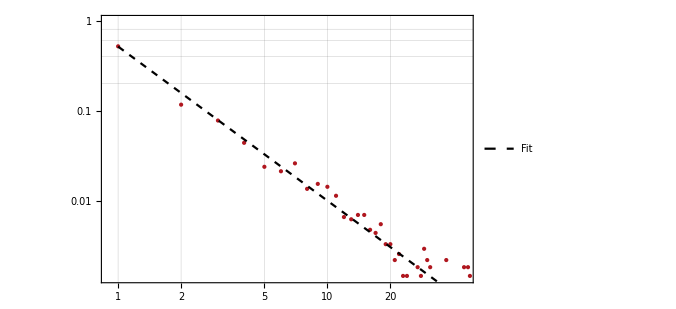

```mathematica
Show[
HistogramPointPlots[sample,
ScalingFunctions->{"Log","Log"},
PlotRange->{{model["xMin"]-0.1,model["xMax"]},{0,1}}
],
Plot[DiscretePowerLawDistributionPDF[model["Alpha"],model["xMin"],model["xMax"],x],{x,model["xMin"],model["xMax"]},
ScalingFunctions->{"Log","Log"},
PlotLegends->{"Fit"},
PlotStyle->{Dashed,Black}
]
]
```